```mathematica
random  = Table[Prepend[RandomInteger[{0,1},4],s],10]
```

{{s,0,0,0,1},{s,1,0,1,0},{s,1,0,0,1},{s,1,1,0,0},{s,0,0,1,0},{s,1,0,0,0},{s,0,0,1,0},{s,0,0,1,1},{s,1,0,0,1},{s,1,0,1,0}}

```mathematica
IntegerDigits[18,2,5]
```

{1,0,0,1,0}

```mathematica
Style[Text[Column[Row/@NestList[Replace[#,{{0,_,_,s___}->{s,0,0},{1,_,_,s___}->{s,1,1,0,1}}]&,IntegerDigits[18,2,5],30]]],FontFamily->"Roboto"]
```

10010
101101
1011101
11011101
111011101
0111011101
101110100
1101001101
10011011101
110111011101
1110111011101
01110111011101
1011101110100
11011101001101
111010011011101
0100110111011101
011011101110100
01110111010000
1011101000000
11010000001101
100000011011101
0000110111011101
011011101110100
01110111010000
1011101000000
11010000001101
100000011011101
0000110111011101
011011101110100
01110111010000
1011101000000

```mathematica
NestList[Replace[{{0,_,_,s___}->{s,0,0},{1,_,_,s___}->{s,1,1,0,1}}],{1,0,0,1,0},10]//Column
```

{1,0,0,1,0}
{1,0,1,1,0,1}
{1,0,1,1,1,0,1}
{1,1,0,1,1,1,0,1}
{1,1,1,0,1,1,1,0,1}
{0,1,1,1,0,1,1,1,0,1}
{1,0,1,1,1,0,1,0,0}
{1,1,0,1,0,0,1,1,0,1}
{1,0,0,1,1,0,1,1,1,0,1}
{1,1,0,1,1,1,0,1,1,1,0,1}
{1,1,1,0,1,1,1,0,1,1,1,0,1}

```mathematica
random = Take[Table[Prepend[RandomInteger[{0,1},4],s],10],1]
```

{{s,1,1,0,1}}

```mathematica
Style[Text[Column[
Row/@NestList[Replace[#,{{0,_,_,s___}->{s,0,0},{1,_,_,s___}->{s,1,1,0,1}}]&,IntegerDigits[1,2,100],30]
]],FontFamily->"Roboto",FontColor->RandomColor[]]
```

0000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000001
000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000100
00000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000010000
0000000000000000000000000000000000000000000000000000000000000000000000000000000000000000001000000
000000000000000000000000000000000000000000000000000000000000000000000000000000000000000100000000
00000000000000000000000000000000000000000000000000000000000000000000000000000000000010000000000
0000000000000000000000000000000000000000000000000000000000000000000000000000000001000000000000
000000000000000000000000000000000000000000000000000000000000000000000000000000100000000000000
00000000000000000000000000000000000000000000000000000000000000000000000000010000000000000000
0000000000000000000000000000000000000000000000000000000000000000000000001000000000000000000
000000000000000000000000000000000000000000000000000000000000000000000100000000000000000000
00000000000000000000000000000000000000000000000000000000000000000010000000000000000000000
0000000000000000000000000000000000000000000000000000000000000001000000000000000000000000
000000000000000000000000000000000000000000000000000000000000100000000000000000000000000
00000000000000000000000000000000000000000000000000000000010000000000000000000000000000
0000000000000000000000000000000000000000000000000000001000000000000000000000000000000
000000000000000000000000000000000000000000000000000100000000000000000000000000000000
00000000000000000000000000000000000000000000000010000000000000000000000000000000000
0000000000000000000000000000000000000000000001000000000000000000000000000000000000
000000000000000000000000000000000000000000100000000000000000000000000000000000000
00000000000000000000000000000000000000010000000000000000000000000000000000000000
0000000000000000000000000000000000001000000000000000000000000000000000000000000
000000000000000000000000000000000100000000000000000000000000000000000000000000
00000000000000000000000000000010000000000000000000000000000000000000000000000
0000000000000000000000000001000000000000000000000000000000000000000000000000
000000000000000000000000100000000000000000000000000000000000000000000000000
00000000000000000000010000000000000000000000000000000000000000000000000000
0000000000000000001000000000000000000000000000000000000000000000000000000
000000000000000100000000000000000000000000000000000000000000000000000000
00000000000010000000000000000000000000000000000000000000000000000000000
0000000001000000000000000000000000000000000000000000000000000000000000

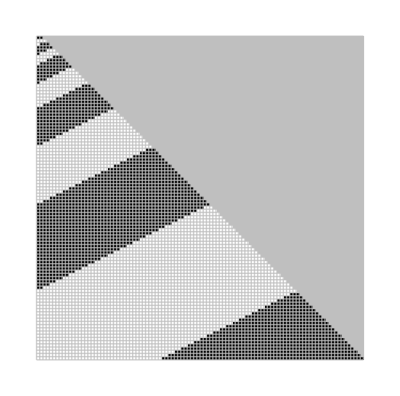

```mathematica
ArrayPlot[PadRight[ResourceFunction["TagSystemEvolveList"][{
{0,0,s___}->{s,1,1,1},{1,0,s___}->{s,1,1,1},{0,1,s___}->{s,1,1,1},{1,1,s___}->{s,0,0,0}
},{1,1},100],Automatic,.25],Mesh->True,MeshStyle->GrayLevel[0.75,0.75]]
```

```mathematica
0
```

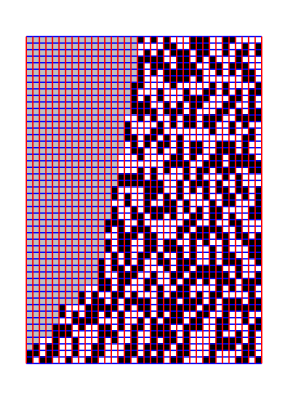

```mathematica
ArrayPlot[Reverse@Transpose[PadRight[NestList[Last[ResourceFunction["TagSystemEvolve"][{{0,0,s___}->{s,0},{1,0,s___}->{s,1,1,1},{0,1,s___}->{s,0,0,0},{1,1,s___}->{s,0,1,1}},#,Quotient[Length[#],2]]]&,{1,1},35],{Automatic,50},.25]],Mesh->True,MeshStyle->{Blue,Red},Frame->False]
```

```mathematica
First[ResourceFunction["TagSystemEvolve"][{{0,0,s___}->{s,0},{1,0,s___}->{s,1,1,0},{0,1,s___}->{s,0,1,1}},#,Quotient[Length[#],2]]] /@0000001
```

1

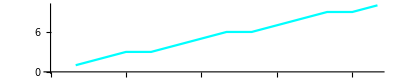

```mathematica
ListLinePlot[
Accumulate[Last[NestList[Replace[#,{{0,_,_,s___}->{s,0,0},{1,_,_,s___}->{s,1,1,0,1}}]&,IntegerDigits[18,2,5],10]]],
AspectRatio->7/35,
PlotStyle->Hue[0.5,1,1]
]
```

```mathematica
2TSDirectEvolveSequence[{1,0,1},10]
```

{2,0,2,2,2,0,2,2,2,0,2,2,2,0,2,0,0,2,2,0,2,0,0,2,2,0,2,0,0,2,2,0,2,0,0}

```mathematica
ListPlot3D[Select[NestList[Replace[#,{{0,_,_,s___}->{s,0,0},{1,_,_,s___}->{s,0,1,0,1,1}}]&,{0,0,1,1},100],Length[#]===4&],Mesh->All]
```

-Graphics3D-

```mathematica
IntegerDigits[18,2,5]
```

{1,0,0,1,0}

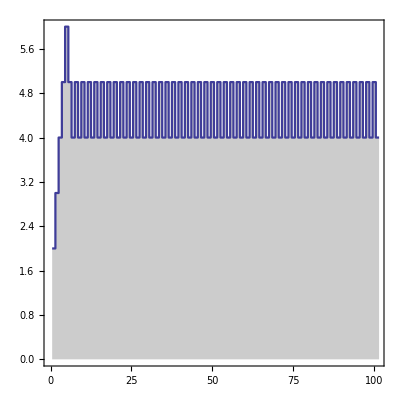

```mathematica
ListStepPlot[ResourceFunction["TagSystemEvolveList"][{{0,0,s___}:>{s,0},{1,0,s___}:>{s,0,1,1},{0,1,s___}:>{s,0,0,0},{1,1,s___}:>{s,1,1,0}},{1,1},100,1,"Lengths"],Center,AspectRatio->1,Filling->Axis,Frame->True,PlotStyle->RGBColor[Red, Green],PlotRange->Full]
```

```mathematica
CloudDeploy[Manipulate[Column[Row/@NestList[Replace[#,{{0,_,_,s___}->{s,0,0},{1,_,_,s___}->{s,1,1,0,1}}]&,IntegerDigits[a,b,c],30]],{a,1,18,1}, {b,2,10,1},{c,1,10,1}], Permissions -> "Public"]
```

CloudObject[https://www.wolframcloud.com/obj/56a3cb36-c8ab-4f2c-8f43-ea59456a2bcd]

```mathematica
IntegerDigits[18,2,5]
```

{1,0,0,1,0}

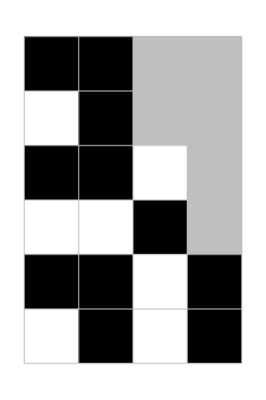
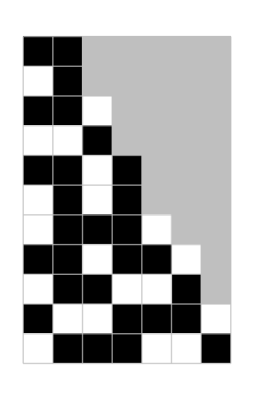
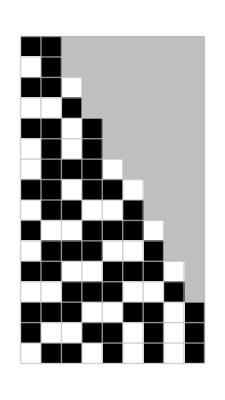
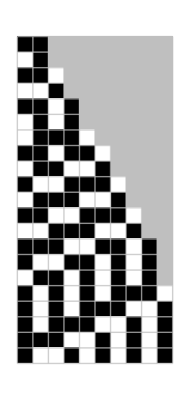
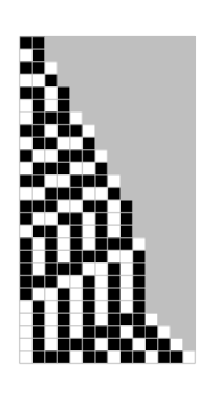
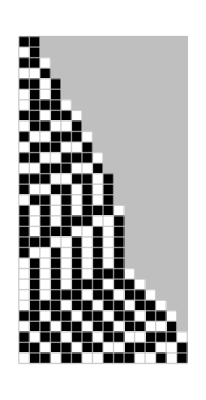
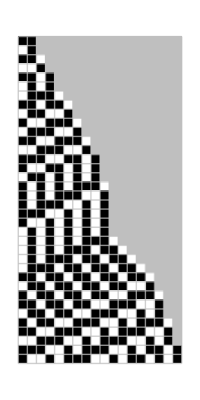
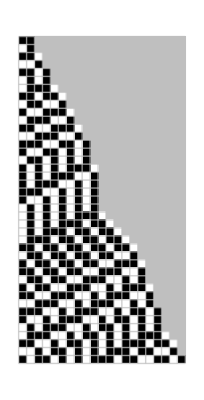

```mathematica
Table[ArrayPlot[PadRight[ResourceFunction["TagSystemEvolveList"][{{0,0,s___}:>{s,1,0,1},{1,0,s___}:>{s,0,1},{0,1,s___}:>{s,1,1,0},{1,1,s___}:>{s,0,1}},{1,1},x],Automatic,.25],Mesh->True,MeshStyle->GrayLevel[0.75,0.75]],{x,5,100,5}]
```

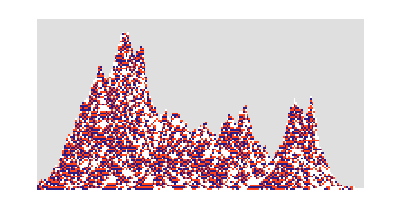

CloudObject[https://www.wolframcloud.com/obj/0fa0c3f8-187e-4e19-bf8f-616a6bf3fcbd]

```mathematica
ArrayPlot[Reverse@Transpose[PadRight[Last[ResourceFunction["TagSystemConvert"][#,2]]&/@NestList[Last[ResourceFunction["TagSystemEvolve"][{{0,_,s___}:>{s,0},{1,_,s___}:>{s,0,2},{2,_,s___}:>{s,2,1,1}},#,Quotient[Length[#],2]]]&,IntegerDigits[546,3,6],180],{Automatic,95},.25]],Frame->False,ColorRules->{0->White,1->Hue[.03,.9,1],2->Hue[.7,.8,.5],-1->GrayLevel[.85]}]
```

```mathematica
CloudDeploy[FormPage[
{"a1"->"Integer","a2"->"Integer","a3"->"Integer","b1"->"Integer","b2"->"Integer","c1"->"Integer","c2"->"Integer","c3"->"Integer","d1"->"Integer","d2"->"Integer"},ArrayPlot[PadRight[ResourceFunction["TagSystemEvolveList"][
{{0,0,s___}:>{s,#a1,#a2,#a3},
{1,0,s___}:>{s,#b1,#b2},
{0,1,s___}:>{s,#c1,#c2,#c3},
{1,1,s___}:>{s,#d1,#d2}},
{1,1},
50],
Automatic,
.25],
Mesh->True,
MeshStyle->GrayLevel[0.75,0.75]]&,
AppearanceRules-><|"ItemLayout"->"Inline"|>],
Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/2ef5fe69-460e-4fdc-b297-962169fc6d81]

```mathematica
CloudDeploy[TabView[Table[NestGraph[ReplaceList[{{left___,0,0,s___}:>{left,s,1,0,1},{left___,1,0,s___}:>{left,s,0,1},{left___,0,1,s___}:>{left,s,1,1,0},{left___,1,1,s___}:>{left,s,0,1}}],{{1,1}},n,VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",PerformanceGoal->"Quality"],{n,10}]],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/b658327e-b2ed-4163-904e-347943542b63]

```mathematica
TabView[Table[ListPlot[Range[20]^n],{n,5}]]
```

12345

```mathematica
Grid[Table[Slider[],4,3]]
```

|  | 
 |  | 
 |  | 
 |  |

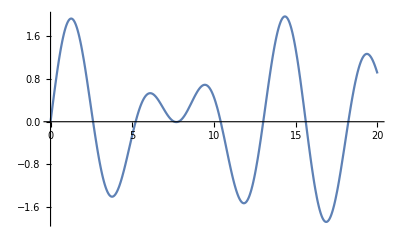

```mathematica
Plot[Sin[x]+Sin[Sqrt[2] x],{x,0,20}]
```

```mathematica
ContourPlot3D[x^3+y^2-z^2,{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

```mathematica
RandomReal[1,{10,3}]
```

{{0.338996,0.256848,0.616389},{0.38158,0.187485,0.768426},{0.919118,0.742005,0.270297},{0.228019,0.30444,0.384496},{0.884658,0.578533,0.0482698},{0.982216,0.00601105,0.88882},{0.237609,0.729119,0.71315},{0.528651,0.360661,0.627237},{0.624004,0.888946,0.556634},{0.554994,0.142034,0.355252}}

```mathematica
ConvexHullMesh[RandomReal[1,{100,3}]]
```

-Graphics3D-

```mathematica
ArrayPlot[CellularAutomaton[30,{{1},0},200]]
```

-Graphics-

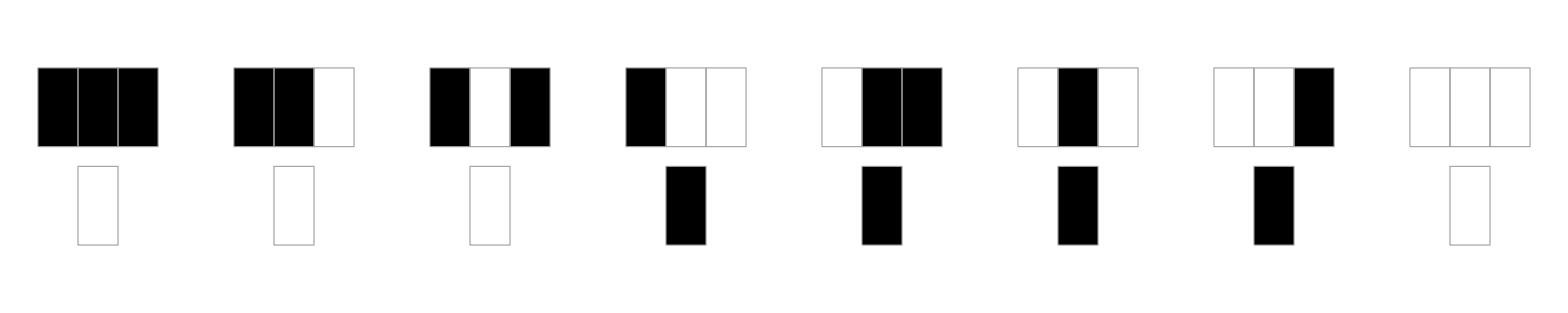

```mathematica
RulePlot[CellularAutomaton[30]]
```

```mathematica
CloudDeploy[FormPage[{"n"->"Integer"},Table[GraphicsRow[{Graphics[Style[Text[Column[Row/@NestList[Replace[#,{{0,_,_,s___}->{s,0,0},{1,_,_,s___}->Table[Prepend[RandomInteger[{0,1},4],s],10][[i]]}]&,IntegerDigits[18,2,5],30]]],FontFamily->"Roboto"],ImageSize-> 3000],Table[Prepend[RandomInteger[{0,1},4],s],10]}],{i,1,#n}]&],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/937ba917-d32b-4344-b3fa-503530c7faea]

```mathematica
NestList[Replace[#,{{0,_,_,s___}->{s,0,0},{1,_,_,s___}->Table[Prepend[RandomInteger[{0,1},4],s],10][[1]]}]&,IntegerDigits[18,2,5],30]
```

{{1,0,0,1,0},{1,0,1,0,1,1},{0,1,1,0,1,1,0},{0,1,1,0,0,0},{0,0,0,0,0},{0,0,0,0},{0,0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

```mathematica
Table[ArrayPlot[Reverse@Transpose[PadRight[Last[ResourceFunction["TagSystemConvert"][#,2]]&/@NestList[Last[ResourceFunction["TagSystemEvolve"][{{0,_,s___}:>{s,0},{1,_,s___}:>{s,0,2},{2,_,s___}:>{s,2,1,1}},#,Quotient[Length[#],2]]]&,IntegerDigits[546,3,6],180],{Automatic,95},.25]],Frame->False,ColorRules->{0->White,1->Hue[.03,.9,1],2->Hue[.7,.8,.5],-1->GrayLevel[.85]}],{i,1,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NestGraph[ReplaceList[{{left___,0,0,s___}:>{left,s,1,0,1},{left___,1,0,s___}:>{left,s,0,1},{left___,0,1,s___}:>{left,s,1,1,0},{left___,1,1,s___}:>{left,s,0,1}}],{{1,1}},7,VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",PerformanceGoal->"Quality"]
```

-Graphics-

```mathematica
(*With[{random=Table[Prepend[RandomInteger[{0,1},4],s],10]},*)
(MapIndexed[{First@#2,#1}&,#]&/@MapAt[Rotate[#,Pi/2]&,{{random[[1]]}},{1,1}])
```

{{{1,{s,1,1,0,0}}}}

{{s,1,0,1,1},{s,0,0,0,0},{s,0,0,0,0},{s,1,0,1,0},{s,0,1,0,0},{s,0,0,0,1},{s,1,1,0,0},{s,0,0,0,1},{s,1,1,0,0},{s,1,1,1,0}}

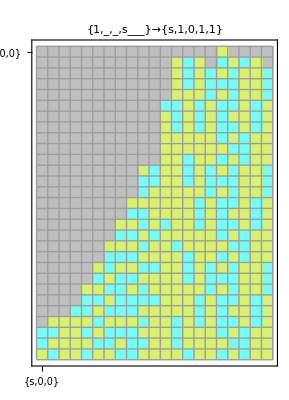
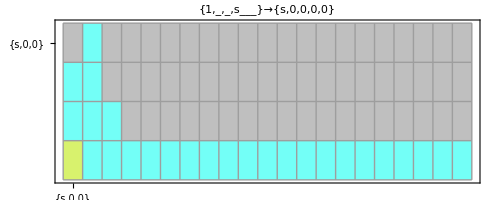
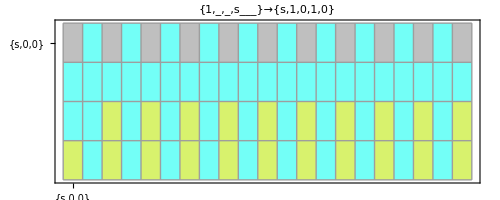
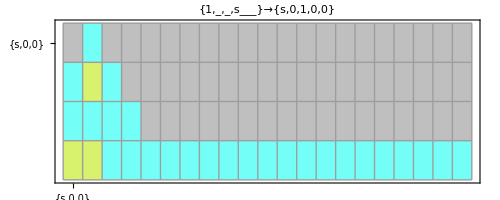
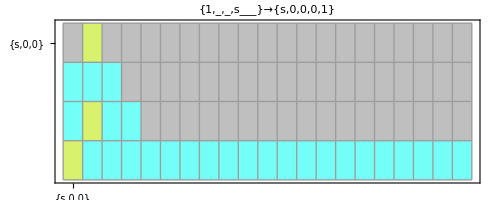
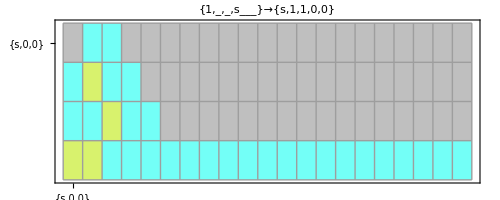
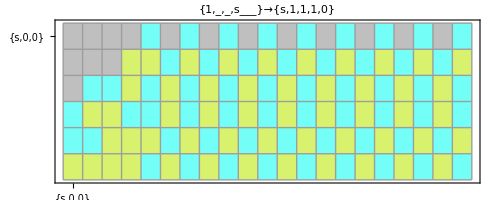
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
random=Table[Prepend[RandomInteger[{0,1},4],s],10]
Table[ArrayPlot[Reverse@Transpose[PadRight[Last[ResourceFunction["TagSystemConvert"][#,2]]&/@NestList[Last[ResourceFunction["TagSystemEvolve"][
{{0,_,_,s___}->{s,0,0},{1,_,_,s___}->random[[i]]},#,Quotient[Length[#],2]
]]&,IntegerDigits[18,2,5],20],{Automatic,Automatic},.25]],Frame->True,ColorRules->{0->Hue[.49,.55,1.43],1->Hue[.2,.55,.95]},Mesh->True,PlotLabel->Style[#,12,FontColor->Hue[.2,.55,.95]]&@({1,_,_,s___}->random[[i]]),FrameTicks->(MapIndexed[{First@#2,#1}&,#]&/@MapAt[Rotate[#,1]&,{{{s,0,0}}},{1,1}]),FrameTicksStyle->Directive[Hue[.49,.55,1.43],12]],{i,1,10}]
```

```mathematica
NestGraph[ReplaceList[{{left___,0,0,s___}:>{left,s,1,0,1},{left___,1,0,s___}:>{left,s,0,1},{left___,0,1,s___}:>{left,s,1,1,0},{left___,1,1,s___}:>{left,s,0,1}}],{{1,1}},7,VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",PerformanceGoal->"Quality"]
```

-Graphics-

{{s,1,1,0,1},{s,1,1,0,0},{s,0,1,1,1},{s,1,0,0,1},{s,1,1,0,1},{s,1,0,0,0},{s,0,1,0,0},{s,1,1,0,0},{s,1,0,1,0},{s,0,0,1,1}}

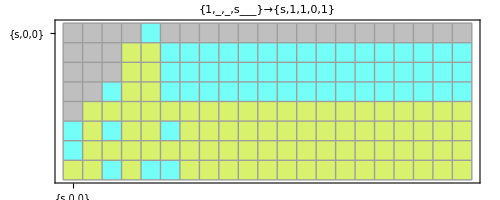
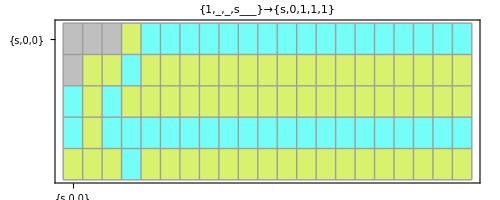
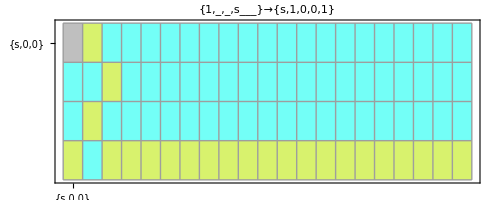
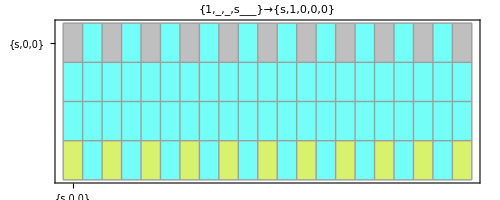
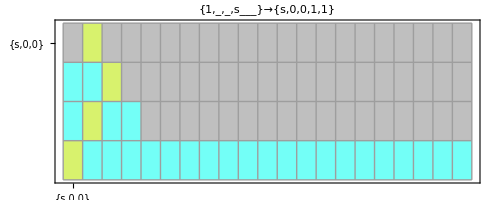
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
random=Table[Prepend[RandomInteger[{0,1},4],s],10]
Table[ArrayPlot[Reverse@Transpose[PadRight[Last[ResourceFunction["TagSystemConvert"][#,2]]&/@NestList[Last[ResourceFunction["TagSystemEvolve"][
{{0,_,_,s___}->{s,0,0},{1,_,_,s___}->random[[i]]},#,Quotient[Length[#],2]
]]&,IntegerDigits[18,2,5],20],{Automatic,Automatic},.25]],Frame->True,ColorRules->{0->Hue[.49,.55,1.43],1->Hue[.2,.55,.95]},Mesh->True,PlotLabel->Style[#,12,FontColor->Hue[.2,.55,.95]]&@({1,_,_,s___}->random[[i]]),FrameTicks->(MapIndexed[{First@#2,#1}&,#]&/@MapAt[Rotate[#,1]&,{{{s,0,0}}},{1,1}]),FrameTicksStyle->Directive[Hue[.49,.55,1.43],12]],{i,1,10}]
```

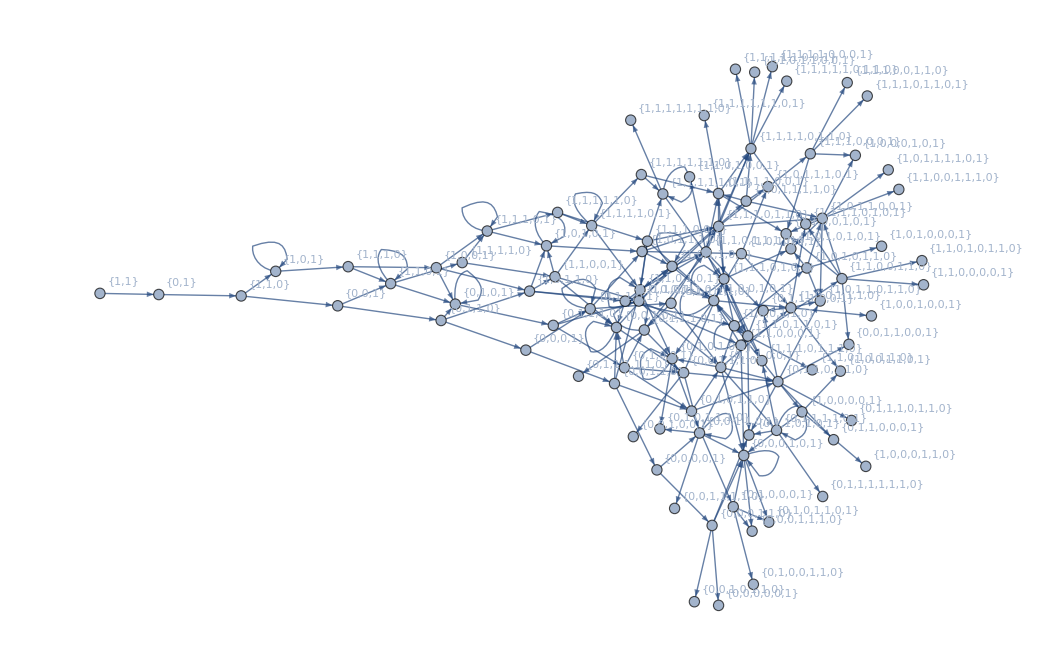

```mathematica
NestGraph[ReplaceList[{{left___,0,0,s___}:>{left,s,1,0,1},{left___,1,0,s___}:>{left,s,0,1},{left___,0,1,s___}:>{left,s,1,1,0},{left___,1,1,s___}:>{left,s,0,1}}],{{1,1}},9,VertexLabels->Automatic]
```

{{0,1},{0,0},{1,1},{1,0},{0,1},{1,0},{0,1},{1,0},{1,1},{0,1}}

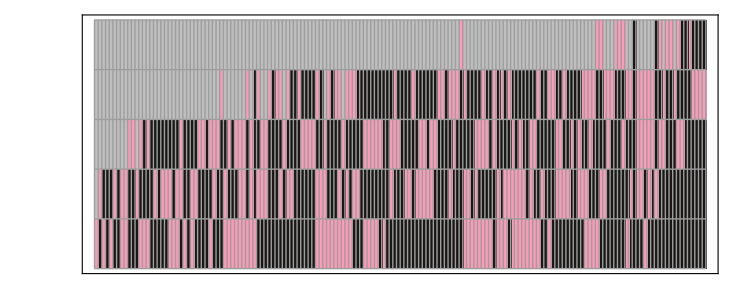
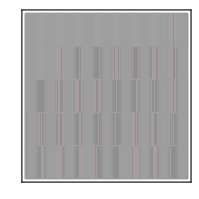
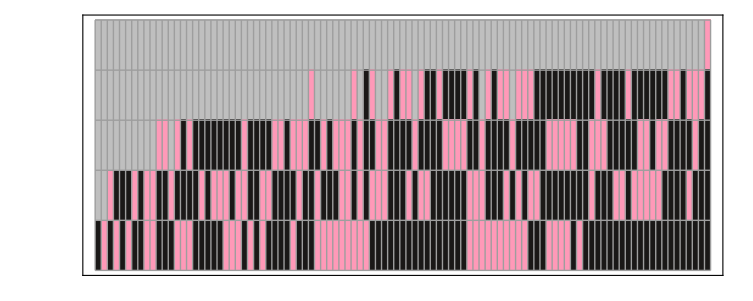
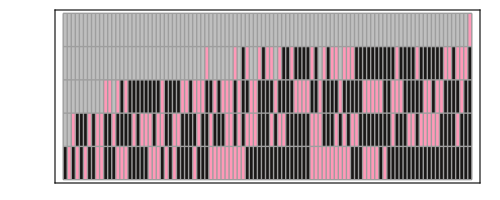
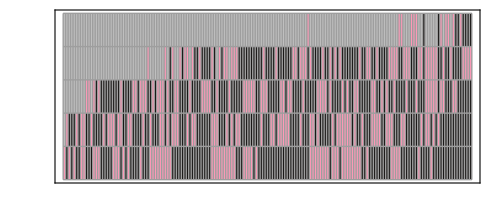
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
randomInit=Table[RandomInteger[{0,1},2],10]
Table[ArrayPlot[Reverse@Transpose[PadRight[Last[ResourceFunction["TagSystemConvert"][#,2]]&/@VertexList[NestGraph[ReplaceList[{{left___,0,0,s___}:>{left,s,1,0,1},{left___,1,0,s___}:>{left,s,0,1},{left___,0,1,s___}:>{left,s,1,1,0},{left___,1,1,s___}:>{left,s,0,1}}],{randomInit[[i]]},9,VertexLabels->Automatic]],{Automatic,Automatic},.25]],Frame->True,ColorRules->{0->Hue[.95,.4,1.4],1->Hue[.1,.1,.1]},Mesh->True],{i,1,10}]
```

```mathematica
NestWhile[IterateState[#[[1]],IterateEdges[ResourceFunction["TagSystemEvolve"][{{0,_,s___}:>{s,0},{1,_,s___}:>{s,0,2},{2,_,s___}:>{s,2,1,1}},#,Quotient[Length[#],2]],#[[2]],
OptionValue[DirectedEdges]]]&,
{{1,0,1},VertexList[ResourceFunction["TagSystemEvolve"][{{0,_,s___}:>{s,0},{1,_,s___}:>{s,0,2},{2,_,s___}:>{s,2,1,1}},#,Quotient[Length[#],2]]]},
ConditionalTest[{##},0,10]&,0,10]
```

{{1,0,1},VertexList[[{{0,_,s___}:>{s,0},{1,_,s___}:>{s,0,2},{2,_,s___}:>{s,2,1,1}},#1,0]]}

```mathematica
NestWhile
```

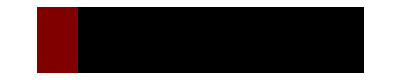
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ArrayPlot[Reverse@Transpose[PadRight[Last[ResourceFunction["TagSystemConvert"][#,2]]&/@NestList[ReplaceList[{{left___,0,0,s___}:>{left,s,1,0,1},{left___,1,0,s___}:>{left,s,0,1},{left___,0,1,s___}:>{left,s,1,1,0},{left___,1,1,s___}:>{left,s,0,1}}],{{1,1}},7],{Automatic,Automatic},.25]],Frame->False,ColorRules->{0->Hue[.49,.55,.43],1->Hue[.98,.66,1]}],{i,1,10}]
```

```mathematica
Table[Graph3D[NestGraph[ReplaceList[{{left___,0,0,s___}:>{left,s,1,0,0},{left___,1,0,s___}:>{left,s,0,1},{left___,0,1,s___}:>{left,s,1,1,0},{left___,1,1,s___}:>{left,s,0,1}}],{{1,0}},t],ImageSize->Small],{t,1,10}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Graph3D[NestGraph[ReplaceList[{{left___,0,0,s___}:>{left,s,1,0,1},{left___,1,0,s___}:>{left,s,0,1},{left___,0,1,s___}:>{left,s,1,1,0},{left___,1,1,s___}:>{left,s,0,1}}],{{0,0,1,0,1,1,0,0,1,0,1,1,1,0,1,1,0,1}},2]]
```

-Graphics3D-

```mathematica
NestList[ReplaceList[{{left___,0,0,s___}:>{left,s,1,0,1},{left___,1,0,s___}:>{left,s,0,1},{left___,0,1,s___}:>{left,s,1,1,0},{left___,1,1,s___}:>{left,s,0,1}}],{{1,1}},7]
```

{{{1,1}},{},{},{},{},{},{},{}}

```mathematica
NestList[Last[ResourceFunction["TagSystemEvolve"][
{{0,_,_,s___}->{s,0,0},{1,_,_,s___}->random[[4]]},#,Quotient[Length[#],2]
]]&,IntegerDigits[18,2,5],20]
```

{{1,0,0,1,0},{0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1,0,0},{0,1,1,1,0,1,1,0,0,1,0,1,1},{1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1},{1,0,0,1,0,1,1,1,0,1,1,1,0,1,1,0,0,1,0,1,1},{0,1,1,1,0,1,1,0,0,0,0,0,0,1,0,1,1,1,0,1,1,1,0,1,1},{0,0,0,1,0,1,1,0,0,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1},{1,1,0,1,1,1,0,1,1,0,0,1,0,1,1,1,0,1,1,1,0,1,1,0,0,1,0,1,1,0,0,1,0,1,1},{1,1,1,0,1,1,1,0,1,1,0,0,1,0,1,1,0,0,1,0,1,1,0,0,1,0,1,1,1,0,1,1,0,0,0,0},{1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,0,0,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,0,0},{1,1,0,0,0,0,0,0,1,0,1,1,1,0,1,1,1,0,1,1,0,0,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,1,0,1,1,0,0,0,0,0,0,1,0,1,1,1,0,1,1},{0,0,1,0,1,1,1,0,1,1,1,0,1,1,0,0,0,0,0,0,1,0,1,1,1,0,1,1,1,0,1,1,0,0,0,0,0,0,1,0,1,1,1,0,1,1,1,0,1,1,0,0,0,0,0,0},{1,1,1,0,1,1,0,0,0,0,0,0,1,0,1,1,1,0,1,1,1,0,1,1,0,0,0,0,0,0,1,0,1,1,1,0,1,1,1,0,1,1,0,0,0,0,0,0,1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1,1,0,1,1,0,0,0,0,0,0,1,0,1,1,1,0,1,1,1,0,1,1,0,0,0,0,0,0,1,0,1,1,1,0,1,1,1,0,1,1,0,0,0,0,0,0},{0,1,1,0,0,0,0,0,0,1,0,1,1,1,0,1,1,1,0,1,1,0,0,0,0,0,0,1,0,1,1,1,0,1,1,1,0,1,1,0,0,0,0,0,0,1,0,1,1,1,0,1,1,1,0,1,1},{1,1,0,1,1,1,0,1,1,0,0,0,0,0,0,1,0,1,1,1,0,1,1,1,0,1,1,0,0,0,0,0,0,1,0,1,1,1,0,1,1,1,0,1,1,0,0,0,0,0,0,1,0,1,1},{0,0,0,0,0,0,1,0,1,1,1,0,1,1,1,0,1,1,0,0,0,0,0,0,1,0,1,1,1,0,1,1,1,0,1,1,0,0,0,0,0,0,1,0,1,1,1,0,1,1,1,0,1,1,0,0},{1,1,1,0,1,1,0,0,0,0,0,0,1,0,1,1,1,0,1,1,1,0,1,1,0,0,0,0,0,0,1,0,1,1,1,0,1,1,1,0,1,1,0,0,0,0,0,0,1,0,1,1,1,0,1,1},{1,0,1,1,1,0,1,1,1,0,1,1,0,0,0,0,0,0,1,0,1,1,1,0,1,1,1,0,1,1,0,0,0,0,0,0,1,0,1,1,1,0,1,1,1,0,1,1,0,0,0,0,0,0}}

```mathematica
Table[Style[Text[Column[Row/@NestList[Replace[#,{{0,_,_,s___}->{s,0,0},{1,_,_,s___}->Table[Prepend[RandomInteger[{0,1},4],s],10][[i]]}]&,IntegerDigits[18,2,5],30]]],FontFamily->"Roboto"],{i,1,10}]
```

{10010
101100
1001010
10100101
001011011
01101100
0110000
000000
00000
0000
000
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00,10010
100111
1110101
01011010
1101000
10000000
000001101
00110100
1010000
00000011
0001100
110000
0000100
010000
00000
0000
000
00
00
00
00
00
00
00
00
00
00
00
00
00
00,10010
101110
1101000
10001110
011100010
10001000
010001010
00101000
0100000
000000
00000
0000
000
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00,10010
101100
1001000
10001000
010000001
00000100
0010000
000000
00000
0000
000
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00,10010
100111
1111000
10001110
011101101
10110100
101001111
0011111001
111100100
1001001100
10011000111
110001110101
0011101010010
110101001000
1010010001111
00100011110011
0001111001100
111100110000
1001100001110
11000011100100
000111001001011
11100100101100
001001011000011
00101100001100
0110000110000
000011000000
01100000000
0000000000
000000000
00000000
0000000,10010
101000
0001000
100000
0001110
111000
0001111
111100
1001111
11110100
101001110
0011100011
110001100
0011000101
100010100
0101001101
100110100
1101000000
10000001000
000010000001
01000000100
0000010000
001000000
00000000
0000000
000000
00000
0000
000
00
00,10010
100000
0000100
010000
00000
0000
000
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00,10010
100011
0111110
111000
0001100
110000
0000111
011100
10000
001100
10000
000011
01100
0000
000
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00,10010
101111
1110000
00001011
0101100
110000
0000101
010100
10000
000000
00000
0000
000
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00,10010
100111
1110001
00011010
1101000
10000111
001111011
11101100
011000001
00000100
0010000
000000
00000
0000
000
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00
00}

```mathematica
Column[ResourceFunction["TagSystemEvolveList"][{{0,0,s___}:>{s,0},{1,0,s___}:>{s,1,0,1},{0,1,s___}:>{s,0,0,0},{1,1,s___}:>{s,0,1,1}},{1,1},289]]
```

{1,1}
{0,1,1}
{1,0,0,0}
{0,0,1,0,1}
{1,0,1,0}
{1,0,1,0,1}
{1,0,1,1,0,1}
{1,1,0,1,1,0,1}
{0,1,1,0,1,0,1,1}
{1,0,1,0,1,1,0,0,0}
{1,0,1,1,0,0,0,1,0,1}
{1,1,0,0,0,1,0,1,1,0,1}
{0,0,0,1,0,1,1,0,1,0,1,1}
{0,1,0,1,1,0,1,0,1,1,0}
{0,1,1,0,1,0,1,1,0,0,0,0}
{1,0,1,0,1,1,0,0,0,0,0,0,0}
{1,0,1,1,0,0,0,0,0,0,0,1,0,1}
{1,1,0,0,0,0,0,0,0,1,0,1,1,0,1}
{0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1}
{0,0,0,0,0,1,0,1,1,0,1,0,1,1,0}
{0,0,0,1,0,1,1,0,1,0,1,1,0,0}
{0,1,0,1,1,0,1,0,1,1,0,0,0}
{0,1,1,0,1,0,1,1,0,0,0,0,0,0}
{1,0,1,0,1,1,0,0,0,0,0,0,0,0,0}
{1,0,1,1,0,0,0,0,0,0,0,0,0,1,0,1}
{1,1,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1}
{0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1}
{0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0}
{0,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0}
{0,0,0,1,0,1,1,0,1,0,1,1,0,0,0}
{0,1,0,1,1,0,1,0,1,1,0,0,0,0}
{0,1,1,0,1,0,1,1,0,0,0,0,0,0,0}
{1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0}
{1,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,1}
{1,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1}
{0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1}
{0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0}
{0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0}
{0,0,0,0,1,0,1,1,0,1,0,1,1,0,0,0}
{0,0,1,0,1,1,0,1,0,1,1,0,0,0,0}
{1,0,1,1,0,1,0,1,1,0,0,0,0,0}
{1,1,0,1,0,1,1,0,0,0,0,0,1,0,1}
{0,1,0,1,1,0,0,0,0,0,1,0,1,0,1,1}
{0,1,1,0,0,0,0,0,1,0,1,0,1,1,0,0,0}
{1,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0}
{0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1}
{0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1,0}
{1,0,1,0,1,1,0,0,0,0,0,0,1,0,1,0,0}
{1,0,1,1,0,0,0,0,0,0,1,0,1,0,0,1,0,1}
{1,1,0,0,0,0,0,0,1,0,1,0,0,1,0,1,1,0,1}
{0,0,0,0,0,0,1,0,1,0,0,1,0,1,1,0,1,0,1,1}
{0,0,0,0,1,0,1,0,0,1,0,1,1,0,1,0,1,1,0}
{0,0,1,0,1,0,0,1,0,1,1,0,1,0,1,1,0,0}
{1,0,1,0,0,1,0,1,1,0,1,0,1,1,0,0,0}
{1,0,0,1,0,1,1,0,1,0,1,1,0,0,0,1,0,1}
{0,1,0,1,1,0,1,0,1,1,0,0,0,1,0,1,1,0,1}
{0,1,1,0,1,0,1,1,0,0,0,1,0,1,1,0,1,0,0,0}
{1,0,1,0,1,1,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0}
{1,0,1,1,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,1,0,1}
{1,1,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,1,0,1,1,0,1}
{0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1}
{0,1,0,1,1,0,1,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0}
{0,1,1,0,1,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0,0,0}
{1,0,1,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0}
{1,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0,1}
{0,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0,1,1,0,1}
{0,0,0,1,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0,1,1,0,1,0}
{0,1,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0}
{0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0}
{1,0,1,0,1,1,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0}
{1,0,1,1,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,1,0,1}
{1,1,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,1,0,1,1,0,1}
{0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1}
{0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0}
{0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0}
{0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0,0}
{0,1,1,0,1,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0,0,0,0,0}
{1,0,1,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0}
{1,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,1,0,1}
{0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1}
{0,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0}
{0,0,0,1,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0}
{0,1,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0}
{0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0}
{1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0}
{1,0,1,1,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,1,0,1}
{1,1,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1}
{0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1}
{0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0}
{0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0}
{0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0,0}
{0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0,0,0}
{0,1,1,0,1,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0}
{1,0,1,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0}
{1,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,1}
{0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1}
{0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0}
{0,0,0,0,1,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0}
{0,0,1,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0}
{1,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0}
{1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,1,0,1}
{0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,1,0,1,0,1,1}
{0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,1,0,1,0,1,1,0,0,0}
{1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1}
{0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1,0}
{0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1,0,0}
{0,0,0,1,0,1,1,0,1,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1,0,0,0}
{0,1,0,1,1,0,1,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1,0,0,0,0}
{0,1,1,0,1,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0}
{1,0,1,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0}
{1,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1}
{0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1}
{0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0}
{0,1,0,1,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0}
{0,1,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0}
{1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1}
{0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0}
{0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0}
{0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0}
{0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0}
{1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0}
{1,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1}
{0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,1}
{0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0}
{0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0}
{0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0}
{0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0}
{0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0}
{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0}
{1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0,1,0,1}
{0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0,1,0,1,1,0,1}
{0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0}
{0,0,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0}
{0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0}
{0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0}
{0,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0}
{1,0,1,0,1,1,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0}
{1,0,1,1,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,1,0,1}
{1,1,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,1,0,1,1,0,1}
{0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1}
{0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0}
{0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0}
{0,0,1,0,1,1,0,1,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0,0}
{1,0,1,1,0,1,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0,0,0}
{1,1,0,1,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0,0,0,1,0,1}
{0,1,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0,0,0,1,0,1,0,1,1}
{0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,0,0,0,0,1,0,1,0,1,1,0,0,0}
{0,0,0,0,1,0,1,1,0,1,0,1,1,0,0,0,0,1,0,1,0,1,1,0,0,0,0}
{0,0,1,0,1,1,0,1,0,1,1,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0}
{1,0,1,1,0,1,0,1,1,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0}
{1,1,0,1,0,1,1,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1}
{0,1,0,1,1,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1,0,1,1}
{0,1,1,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0}
{1,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0}
{0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1}
{0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1,0}
{0,1,0,1,1,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1,0,0,0,0}
{0,1,1,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0}
{1,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1}
{0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0}
{0,1,0,1,0,1,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0}
{0,1,0,1,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0}
{0,1,1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0}
{1,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1}
{0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0}
{0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0}
{0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0}
{0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0}
{1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0}
{1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1}
{0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1}
{0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0}
{0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0}
{0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0}
{0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0}
{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0}
{1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0,1}
{0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,1,0,1}
{0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,1,0,1,0}
{0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,1,0,1,0,0}
{0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,1,0,1,0,0,0}
{0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0}
{0,0,1,0,1,1,0,1,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0}
{1,0,1,1,0,1,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0}
{1,1,0,1,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,1,0,1}
{0,1,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,1,0,1,0,1,1}
{0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0}
{0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0}
{0,1,0,1,1,0,1,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0}
{0,1,1,0,1,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0}
{1,0,1,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0}
{1,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1}
{0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1}
{0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0}
{0,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0}
{0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0}
{0,1,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0}
{1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1}
{0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0}
{0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0}
{0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0}
{0,0,1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0}
{1,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0}
{1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,1}
{0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,1,0,1,1}
{0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,1,0,1,1,0,0,0}
{0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0}
{0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0}
{0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0}
{0,0,0,1,0,1,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0}
{0,1,0,1,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0}
{0,1,0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
{0,0,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
{0,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
{0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
{0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1}
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0}
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0}
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0}
{0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0}
{0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0}
{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0}
{1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1}
{0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1}
{0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0}
{0,0,0,0,0,0,0,1,0,1,1,0,1,0,0}
{0,0,0,0,0,1,0,1,1,0,1,0,0,0}
{0,0,0,1,0,1,1,0,1,0,0,0,0}
{0,1,0,1,1,0,1,0,0,0,0,0}
{0,1,1,0,1,0,0,0,0,0,0,0,0}
{1,0,1,0,0,0,0,0,0,0,0,0,0,0}
{1,0,0,0,0,0,0,0,0,0,0,0,1,0,1}
{0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1}
{0,0,0,0,0,0,0,0,1,0,1,1,0,1,0}
{0,0,0,0,0,0,1,0,1,1,0,1,0,0}
{0,0,0,0,1,0,1,1,0,1,0,0,0}
{0,0,1,0,1,1,0,1,0,0,0,0}
{1,0,1,1,0,1,0,0,0,0,0}
{1,1,0,1,0,0,0,0,0,1,0,1}
{0,1,0,0,0,0,0,1,0,1,0,1,1}
{0,0,0,0,0,1,0,1,0,1,1,0,0,0}
{0,0,0,1,0,1,0,1,1,0,0,0,0}
{0,1,0,1,0,1,1,0,0,0,0,0}
{0,1,0,1,1,0,0,0,0,0,0,0,0}
{0,1,1,0,0,0,0,0,0,0,0,0,0,0}
{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1}
{0,0,0,0,0,0,0,0,0,0,0,1,0,1,0}
{0,0,0,0,0,0,0,0,0,1,0,1,0,0}
{0,0,0,0,0,0,0,1,0,1,0,0,0}
{0,0,0,0,0,1,0,1,0,0,0,0}
{0,0,0,1,0,1,0,0,0,0,0}
{0,1,0,1,0,0,0,0,0,0}
{0,1,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0}
{0,0,0,0,0,0}
{0,0,0,0,0}
{0,0,0,0}
{0,0,0}
{0,0}
{0}